```mathematica
Clear[Dz,Dzo,Dza,Dze,Dzx,dza]
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
FI[n_]:=FactorInteger[n];FI[1]:={}
dza[n_,z_,a_]:=dza[n,z,a]=Product[rise[z,p[[2]],a]/p[[2]]!,{p,FI[n]}]
rise[z_,k_]:= rise[z,k]=Product[ z+j,{j,0,k-1}]
rise[z_,k_,a_]:= rise[z,k,a]=Product[ z+j a,{j,0,k-1}]
Dz[n_,z_,y_]:=Dz[n,z,y]=If[n<y,1,Sum[bin[z,k]Dz[n/y^k, z-k, y+1],{k,0,Log[y,n]}]]
Dzo[n_,z_,y_]:=Dzo[n,z,y]=If[n<y,1, Dzo[n, z, y+1]+Sum[z^k/k! Dzo[n/y^k, z-k, y+1],{k,1,Log[y,n]}]]
Dza[n_,z_,y_]:=Dza[n,z,y]=If[n<y,1,Sum[Pochhammer[z,k]/k! Dza[n/y^k, z-k, y+1],{k,0,Log[y,n]}]]
Dze[n_,z_,y_]:=Dze[n,z,y]=If[n<y,1,Sum[(-1)^k Pochhammer[-z,k]/k! Dze[n/y^k, z-k, y+1],{k,0,Log[y,n]}]]
Dzx[n_,a_,z_,y_]:=Dzx[n,a,z,y]=If[n<y,1,Sum[rise[z,k,a]/k! Dzx[n/y^k,a, z-k, y+1],{k,0,Log[y,n]}]]
dzx[n_,a_,z_]:=Dzx[n,a,z,2]-Dzx[n-1,a,z,2]
ldzx[n_,a_]:=D[dzx[n,a,z],z]/.z->0
```

```mathematica
Expand@Dz[100,z,2]
```

1+(428 z)/15+(16289 z^2)/360+(331 z^3)/16+(611 z^4)/144+(67 z^5)/240+(7 z^6)/720

```mathematica
Expand@Dzo[100,z,2]
```

1+(161 z)/6+37 z^2+(93 z^3)/4+(16 z^4)/3+(23 z^5)/60+(7 z^6)/720

```mathematica
Expand@Dza[100,z,2]
```

1+(193 z)/15+(6389 z^2)/360+(1375 z^3)/48+(1043 z^4)/144+(39 z^5)/80+(7 z^6)/720

```mathematica
Expand@Dze[100,z,2]
```

1+(428 z)/15+(16289 z^2)/360+(331 z^3)/16+(611 z^4)/144+(67 z^5)/240+(7 z^6)/720

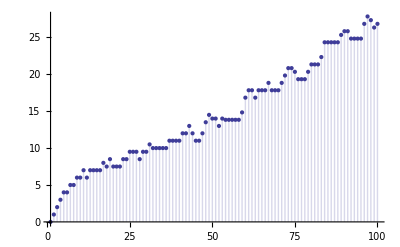

```mathematica
DiscretePlot[D[ Dzo[n,z,2],z]/.z->0,{n,1,100}]
```

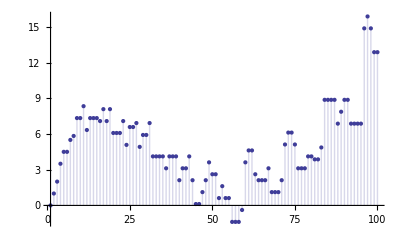

```mathematica
DiscretePlot[ D[Dza[n,z,2],z]/.z->0,{n,1,100}]
```

```mathematica
Table[{n,ldzx[n,-3],ldzx[n,-2],ldzx[n,-1], ldzx[n,0], ldzx[n,1],ldzx[n,2],ldzx[n,3]},{n,1,100}]//TableForm
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | -1/2 | 0 | 1/2 | 1 | 3/2 | 2 | 5/2
5 | 1 | 1 | 1 | 1 | 1 | 1 | 1
6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 1 | 1 | 1 | 1 | 1 | 1 | 1
8 | 3 | 4/3 | 1/3 | 0 | 1/3 | 4/3 | 3
9 | -1/2 | 0 | 1/2 | 1 | 3/2 | 2 | 5/2
10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11 | 1 | 1 | 1 | 1 | 1 | 1 | 1
12 | 2 | 1 | 0 | -1 | -2 | -3 | -4
13 | 1 | 1 | 1 | 1 | 1 | 1 | 1
14 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16 | -21/4 | -1 | 1/4 | 0 | -1/4 | 1 | 21/4
17 | 1 | 1 | 1 | 1 | 1 | 1 | 1
18 | 1 | 1/2 | 0 | -1/2 | -1 | -3/2 | -2
19 | 1 | 1 | 1 | 1 | 1 | 1 | 1
20 | 2 | 1 | 0 | -1 | -2 | -3 | -4
21 | 0 | 0 | 0 | 0 | 0 | 0 | 0
22 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23 | 1 | 1 | 1 | 1 | 1 | 1 | 1
24 | -6 | -2 | 0 | 0 | -2 | -6 | -12
25 | -1/2 | 0 | 1/2 | 1 | 3/2 | 2 | 5/2
26 | 0 | 0 | 0 | 0 | 0 | 0 | 0
27 | 3 | 4/3 | 1/3 | 0 | 1/3 | 4/3 | 3
28 | 2 | 1 | 0 | -1 | -2 | -3 | -4
29 | 1 | 1 | 1 | 1 | 1 | 1 | 1
30 | 0 | 0 | 0 | 0 | 0 | 0 | 0
31 | 1 | 1 | 1 | 1 | 1 | 1 | 1
32 | 56/5 | 17/10 | 1/5 | -1/2 | -14/5 | -43/10 | 11/5
33 | 0 | 0 | 0 | 0 | 0 | 0 | 0
34 | 0 | 0 | 0 | 0 | 0 | 0 | 0
35 | 0 | 0 | 0 | 0 | 0 | 0 | 0
36 | -3 | -1 | 0 | 0 | -1 | -3 | -6
37 | 1 | 1 | 1 | 1 | 1 | 1 | 1
38 | 0 | 0 | 0 | 0 | 0 | 0 | 0
39 | 0 | 0 | 0 | 0 | 0 | 0 | 0
40 | -6 | -2 | 0 | 0 | -2 | -6 | -12
41 | 1 | 1 | 1 | 1 | 1 | 1 | 1
42 | 0 | 0 | 0 | 0 | 0 | 0 | 0
43 | 1 | 1 | 1 | 1 | 1 | 1 | 1
44 | 2 | 1 | 0 | -1 | -2 | -3 | -4
45 | 2 | 1 | 0 | -1 | -2 | -3 | -4
46 | 0 | 0 | 0 | 0 | 0 | 0 | 0
47 | 1 | 1 | 1 | 1 | 1 | 1 | 1
48 | 15 | 5/2 | 0 | 3/2 | 1 | -15/2 | -30
49 | -1/2 | 0 | 1/2 | 1 | 3/2 | 2 | 5/2
50 | 1 | 1/2 | 0 | -1/2 | -1 | -3/2 | -2
51 | 0 | 0 | 0 | 0 | 0 | 0 | 0
52 | 2 | 1 | 0 | -1 | -2 | -3 | -4
53 | 1 | 1 | 1 | 1 | 1 | 1 | 1
54 | -5/3 | -1/2 | 0 | -1/6 | -1 | -5/2 | -14/3
55 | 0 | 0 | 0 | 0 | 0 | 0 | 0
56 | -6 | -2 | 0 | 0 | -2 | -6 | -12
57 | 0 | 0 | 0 | 0 | 0 | 0 | 0
58 | 0 | 0 | 0 | 0 | 0 | 0 | 0
59 | 1 | 1 | 1 | 1 | 1 | 1 | 1
60 | -4 | -2 | 0 | 2 | 4 | 6 | 8
61 | 1 | 1 | 1 | 1 | 1 | 1 | 1
62 | 0 | 0 | 0 | 0 | 0 | 0 | 0
63 | 2 | 1 | 0 | -1 | -2 | -3 | -4
64 | -49/2 | -2 | 1/6 | 1 | -1/2 | -16/3 | 11/2
65 | 0 | 0 | 0 | 0 | 0 | 0 | 0
66 | 0 | 0 | 0 | 0 | 0 | 0 | 0
67 | 1 | 1 | 1 | 1 | 1 | 1 | 1
68 | 2 | 1 | 0 | -1 | -2 | -3 | -4
69 | 0 | 0 | 0 | 0 | 0 | 0 | 0
70 | 0 | 0 | 0 | 0 | 0 | 0 | 0
71 | 1 | 1 | 1 | 1 | 1 | 1 | 1
72 | 13 | 3 | 0 | 1 | 3 | 3 | -2
73 | 1 | 1 | 1 | 1 | 1 | 1 | 1
74 | 0 | 0 | 0 | 0 | 0 | 0 | 0
75 | 1 | 1/2 | 0 | -1/2 | -1 | -3/2 | -2
76 | 2 | 1 | 0 | -1 | -2 | -3 | -4
77 | 0 | 0 | 0 | 0 | 0 | 0 | 0
78 | 0 | 0 | 0 | 0 | 0 | 0 | 0
79 | 1 | 1 | 1 | 1 | 1 | 1 | 1
80 | 16 | 3 | 0 | 1 | 0 | -9 | -32
81 | -21/4 | -1 | 1/4 | 0 | -1/4 | 1 | 21/4
82 | 0 | 0 | 0 | 0 | 0 | 0 | 0
83 | 1 | 1 | 1 | 1 | 1 | 1 | 1
84 | -4 | -2 | 0 | 2 | 4 | 6 | 8
85 | 0 | 0 | 0 | 0 | 0 | 0 | 0
86 | 0 | 0 | 0 | 0 | 0 | 0 | 0
87 | 0 | 0 | 0 | 0 | 0 | 0 | 0
88 | -6 | -2 | 0 | 0 | -2 | -6 | -12
89 | 1 | 1 | 1 | 1 | 1 | 1 | 1
90 | -1 | -1/2 | 0 | 1/2 | 1 | 3/2 | 2
91 | 0 | 0 | 0 | 0 | 0 | 0 | 0
92 | 2 | 1 | 0 | -1 | -2 | -3 | -4
93 | 0 | 0 | 0 | 0 | 0 | 0 | 0
94 | 0 | 0 | 0 | 0 | 0 | 0 | 0
95 | 0 | 0 | 0 | 0 | 0 | 0 | 0
96 | -40 | -4 | 0 | 2 | 8 | 0 | -64
97 | 1 | 1 | 1 | 1 | 1 | 1 | 1
98 | 1 | 1/2 | 0 | -1/2 | -1 | -3/2 | -2
99 | 2 | 1 | 0 | -1 | -2 | -3 | -4
100 | -4 | -3/2 | 0 | 1/2 | 0 | -3/2 | -4

```mathematica
rise[z,3,0]
```

z^3

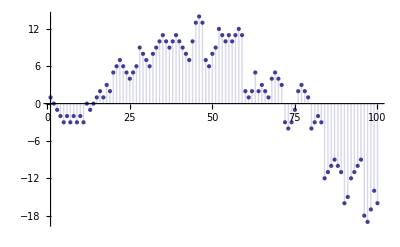

```mathematica
DiscretePlot[Dzx[n,1,-1,2],{n,1,100}]
```

```mathematica
Grid@Table[dzx[n,k,-1],{n,1,100},{k,-3,3}]
```

0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 1/2 | 0 | -1/2 | -1 | -3/2 | -2
-1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 1 | 1 | 1 | 1 | 1 | 1
-1 | -1 | -1 | -1 | -1 | -1 | -1
-11/3 | -3/2 | 0 | 5/6 | 1 | 1/2 | -2/3
1 | 1/2 | 0 | -1/2 | -1 | -3/2 | -2
1 | 1 | 1 | 1 | 1 | 1 | 1
-1 | -1 | -1 | -1 | -1 | -1 | -1
-3 | -3/2 | 0 | 3/2 | 3 | 9/2 | 6
-1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1
26/3 | 19/8 | 0 | 1/24 | 1 | 11/8 | -1/3
-1 | -1 | -1 | -1 | -1 | -1 | -1
-2 | -1 | 0 | 1 | 2 | 3 | 4
-1 | -1 | -1 | -1 | -1 | -1 | -1
-3 | -3/2 | 0 | 3/2 | 3 | 9/2 | 6
1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1
-1 | -1 | -1 | -1 | -1 | -1 | -1
35/3 | 9/2 | 0 | -11/6 | -1 | 5/2 | 26/3
1 | 1/2 | 0 | -1/2 | -1 | -3/2 | -2
1 | 1 | 1 | 1 | 1 | 1 | 1
-11/3 | -3/2 | 0 | 5/6 | 1 | 1/2 | -2/3
-3 | -3/2 | 0 | 3/2 | 3 | 9/2 | 6
-1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1
-59/3 | -27/8 | 0 | 19/120 | 2 | 45/8 | 19/3
1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1
7 | 11/4 | 0 | -5/4 | -1 | 3/4 | 4
-1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1
35/3 | 9/2 | 0 | -11/6 | -1 | 5/2 | 26/3
-1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1
-3 | -3/2 | 0 | 3/2 | 3 | 9/2 | 6
-3 | -3/2 | 0 | 3/2 | 3 | 9/2 | 6
1 | 1 | 1 | 1 | 1 | 1 | 1
-1 | -1 | -1 | -1 | -1 | -1 | -1
-95/3 | -59/8 | 0 | -49/24 | -6 | -35/8 | 31/3
1 | 1/2 | 0 | -1/2 | -1 | -3/2 | -2
-2 | -1 | 0 | 1 | 2 | 3 | 4
1 | 1 | 1 | 1 | 1 | 1 | 1
-3 | -3/2 | 0 | 3/2 | 3 | 9/2 | 6
-1 | -1 | -1 | -1 | -1 | -1 | -1
19/3 | 5/2 | 0 | -7/6 | -1 | 1/2 | 10/3
1 | 1 | 1 | 1 | 1 | 1 | 1
35/3 | 9/2 | 0 | -11/6 | -1 | 5/2 | 26/3
1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1
-1 | -1 | -1 | -1 | -1 | -1 | -1
9 | 9/2 | 0 | -9/2 | -9 | -27/2 | -18
-1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 1 | 1 | 1 | 1 | 1 | 1
-3 | -3/2 | 0 | 3/2 | 3 | 9/2 | 6
428/9 | 85/16 | 0 | -1049/720 | -3 | 9/16 | 32/9
1 | 1 | 1 | 1 | 1 | 1 | 1
-1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1
-3 | -3/2 | 0 | 3/2 | 3 | 9/2 | 6
1 | 1 | 1 | 1 | 1 | 1 | 1
-1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1
-86/3 | -8 | 0 | -2/3 | -6 | -12 | -44/3
-1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 1 | 1 | 1 | 1 | 1 | 1
-2 | -1 | 0 | 1 | 2 | 3 | 4
-3 | -3/2 | 0 | 3/2 | 3 | 9/2 | 6
1 | 1 | 1 | 1 | 1 | 1 | 1
-1 | -1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | -1 | -1
-98/3 | -63/8 | 0 | -37/24 | -5 | -23/8 | 37/3
26/3 | 19/8 | 0 | 1/24 | 1 | 11/8 | -1/3
1 | 1 | 1 | 1 | 1 | 1 | 1
-1 | -1 | -1 | -1 | -1 | -1 | -1
9 | 9/2 | 0 | -9/2 | -9 | -27/2 | -18
1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1
35/3 | 9/2 | 0 | -11/6 | -1 | 5/2 | 26/3
-1 | -1 | -1 | -1 | -1 | -1 | -1
5 | 5/2 | 0 | -5/2 | -5 | -15/2 | -10
1 | 1 | 1 | 1 | 1 | 1 | 1
-3 | -3/2 | 0 | 3/2 | 3 | 9/2 | 6
1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1
88 | 99/8 | 0 | 7/40 | -9 | -165/8 | 1
-1 | -1 | -1 | -1 | -1 | -1 | -1
-2 | -1 | 0 | 1 | 2 | 3 | 4
-3 | -3/2 | 0 | 3/2 | 3 | 9/2 | 6
8 | 13/4 | 0 | -7/4 | -2 | -3/4 | 2

```mathematica
Grid@Table[dzx[n,k,z],{n,1,20},{k,-2,2}]
```

0 | 0 | 0 | 0 | 0
z | z | z | z | z
z | z | z | z | z
z+1/2 (-2+z) z | z+1/2 (-1+z) z | z+z^2/2 | z+1/2 z (1+z) | z+1/2 z (2+z)
z | z | z | z | z
z^2 | z^2 | z^2 | z^2 | z^2
z | z | z | z | z
z+1/6 (-4+z) (-2+z) z-z^2+z (-1+2 z) | z+1/6 (-2+z) (-1+z) z-z^2+z (-1+2 z) | z-z^2+z^3/6+z (-1+2 z) | z-z^2+1/6 z (1+z) (2+z)+z (-1+2 z) | z-z^2+1/6 z (2+z) (4+z)+z (-1+2 z)
z+1/2 (-2+z) z | z+1/2 (-1+z) z | z+z^2/2 | z+1/2 z (1+z) | z+1/2 z (2+z)
z-z (-1+2 z)+z (-2+3 z) | z-z (-1+2 z)+z (-2+3 z) | z-z (-1+2 z)+z (-2+3 z) | z-z (-1+2 z)+z (-2+3 z) | z-z (-1+2 z)+z (-2+3 z)
z | z | z | z | z
-1/2 (-2+z) z+1/2 (-2+z) (-1+z) z+z^2-z (-2+3 z)+z (-3+4 z) | -1/2 (-1+z) z+1/2 (-1+z)^2 z+z^2-z (-2+3 z)+z (-3+4 z) | z^2/2+1/2 (-1+z) z^2-z (-2+3 z)+z (-3+4 z) | z^2-1/2 z (1+z)+1/2 (-1+z) z (1+z)-z (-2+3 z)+z (-3+4 z) | z^2-1/2 z (2+z)+1/2 (-1+z) z (2+z)-z (-2+3 z)+z (-3+4 z)
z | z | z | z | z
z-z (-3+4 z)+z (-4+5 z) | z-z (-3+4 z)+z (-4+5 z) | z-z (-3+4 z)+z (-4+5 z) | z-z (-3+4 z)+z (-4+5 z) | z-z (-3+4 z)+z (-4+5 z)
z-z^2+z (-1+2 z) | z-z^2+z (-1+2 z) | z-z^2+z (-1+2 z) | z-z^2+z (-1+2 z) | z-z^2+z (-1+2 z)
z+1/2 (-2+z) z+1/24 (-6+z) (-4+z) (-2+z) z-1/2 (-2+z) (-1+z) z+1/2 (-2+z) z (-3+2 z)-z (-4+5 z)+z (-5+6 z) | z+1/2 (-1+z) z+1/24 (-3+z) (-2+z) (-1+z) z-1/2 (-1+z)^2 z+1/2 (-1+z) z (-3+2 z)-z (-4+5 z)+z (-5+6 z) | z+z^2/2-1/2 (-1+z) z^2+z^4/24+1/2 z^2 (-3+2 z)-z (-4+5 z)+z (-5+6 z) | z+1/2 z (1+z)-1/2 (-1+z) z (1+z)+1/24 z (1+z) (2+z) (3+z)+1/2 z (1+z) (-3+2 z)-z (-4+5 z)+z (-5+6 z) | z+1/2 z (2+z)-1/2 (-1+z) z (2+z)+1/24 z (2+z) (4+z) (6+z)+1/2 z (2+z) (-3+2 z)-z (-4+5 z)+z (-5+6 z)
z | z | z | z | z
z-z (-1+2 z)+z (-2+3 z)-z (-5+6 z)+z (-6+1/2 (-3+z) (-1+z)+7 z) | z-z (-1+2 z)+z (-2+3 z)-z (-5+6 z)+z (-6+1/2 (-2+z) (-1+z)+7 z) | z-z (-1+2 z)+z (-2+3 z)-z (-5+6 z)+z (-6+1/2 (-1+z)^2+7 z) | z-z (-1+2 z)+z (-2+3 z)-z (-5+6 z)+z (-6+7 z+1/2 (-1+z) z) | z-z (-1+2 z)+z (-2+3 z)-z (-5+6 z)+z (-6+7 z+1/2 (-1+z) (1+z))
z | z | z | z | z
z^2-1/2 (-2+z) z (-3+2 z)+1/2 (-2+z) z (-5+3 z)-z (-6+1/2 (-3+z) (-1+z)+7 z)+z (-7+1/2 (-3+z) (-1+z)+8 z) | z^2-1/2 (-1+z) z (-3+2 z)+1/2 (-1+z) z (-5+3 z)-z (-6+1/2 (-2+z) (-1+z)+7 z)+z (-7+1/2 (-2+z) (-1+z)+8 z) | z^2-1/2 z^2 (-3+2 z)+1/2 z^2 (-5+3 z)-z (-6+1/2 (-1+z)^2+7 z)+z (-7+1/2 (-1+z)^2+8 z) | z^2-1/2 z (1+z) (-3+2 z)+1/2 z (1+z) (-5+3 z)-z (-6+7 z+1/2 (-1+z) z)+z (-7+8 z+1/2 (-1+z) z) | z^2-1/2 z (2+z) (-3+2 z)+1/2 z (2+z) (-5+3 z)-z (-6+7 z+1/2 (-1+z) (1+z))+z (-7+8 z+1/2 (-1+z) (1+z))

```mathematica
$RecursionLimit=10000
```

10000

```mathematica
Expand[dzx[16,0,z]dzx[27,0,z]]
```

z^4/2+(7 z^5)/12+z^6/8+z^7/144

```mathematica
Expand[dzx[16 27,0,z]]
```

-4 z+(11 z^2)/3+(25 z^3)/12-(37 z^4)/36+z^5/4+z^6/8+z^7/144

```mathematica
(* Only -1 is multiplicative*)
```

```mathematica
Grid@Table[dza[n,z,k],{n,1,20},{k,-2,2}]
```

1 | 1 | 1 | 1 | 1
z | z | z | z | z
z | z | z | z | z
1/2 (-2+z) z | 1/2 (-1+z) z | z^2/2 | 1/2 z (1+z) | 1/2 z (2+z)
z | z | z | z | z
z^2 | z^2 | z^2 | z^2 | z^2
z | z | z | z | z
1/6 (-4+z) (-2+z) z | 1/6 (-2+z) (-1+z) z | z^3/6 | 1/6 z (1+z) (2+z) | 1/6 z (2+z) (4+z)
1/2 (-2+z) z | 1/2 (-1+z) z | z^2/2 | 1/2 z (1+z) | 1/2 z (2+z)
z^2 | z^2 | z^2 | z^2 | z^2
z | z | z | z | z
1/2 (-2+z) z^2 | 1/2 (-1+z) z^2 | z^3/2 | 1/2 z^2 (1+z) | 1/2 z^2 (2+z)
z | z | z | z | z
z^2 | z^2 | z^2 | z^2 | z^2
z^2 | z^2 | z^2 | z^2 | z^2
1/24 (-6+z) (-4+z) (-2+z) z | 1/24 (-3+z) (-2+z) (-1+z) z | z^4/24 | 1/24 z (1+z) (2+z) (3+z) | 1/24 z (2+z) (4+z) (6+z)
z | z | z | z | z
1/2 (-2+z) z^2 | 1/2 (-1+z) z^2 | z^3/2 | 1/2 z^2 (1+z) | 1/2 z^2 (2+z)
z | z | z | z | z
1/2 (-2+z) z^2 | 1/2 (-1+z) z^2 | z^3/2 | 1/2 z^2 (1+z) | 1/2 z^2 (2+z)

```mathematica
dza[12,z,1]
```

1/2 z^2 (1+z)

```mathematica
dzx[12,-1,z]
```

-1/2 (-1+z) z+1/2 (-1+z)^2 z+z^2-z (-2+3 z)+z (-3+4 z)

```mathematica
Grid@Table[D[dza[n,z,k],z]/.z->0,{n,1,100},{k,-4,4}]
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
-2 | -3/2 | -1 | -1/2 | 0 | 1/2 | 1 | 3/2 | 2
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
16/3 | 3 | 4/3 | 1/3 | 0 | 1/3 | 4/3 | 3 | 16/3
-2 | -3/2 | -1 | -1/2 | 0 | 1/2 | 1 | 3/2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-16 | -27/4 | -2 | -1/4 | 0 | 1/4 | 2 | 27/4 | 16
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | -3/2 | -1 | -1/2 | 0 | 1/2 | 1 | 3/2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16/3 | 3 | 4/3 | 1/3 | 0 | 1/3 | 4/3 | 3 | 16/3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
256/5 | 81/5 | 16/5 | 1/5 | 0 | 1/5 | 16/5 | 81/5 | 256/5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | -3/2 | -1 | -1/2 | 0 | 1/2 | 1 | 3/2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-512/3 | -81/2 | -16/3 | -1/6 | 0 | 1/6 | 16/3 | 81/2 | 512/3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-16 | -27/4 | -2 | -1/4 | 0 | 1/4 | 2 | 27/4 | 16
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
Sum[ Binomial[z,k] (x-1)^k,{k,0,Infinity}]
```

x^z

```mathematica
Sum[z^k/k! (x-1)^k,{k,0,Infinity}]
```

ⅇ^((-1+x) z)

```mathematica
Sum[Pochhammer[z,k]/k! (x+1)^k,{k,0,Infinity}]
```

(-x)^-z

```mathematica
D[Sum[Pochhammer[z,k]/k! (x+1)^k,{k,0,Infinity}],z]/.z->0
```

-Log[-x]

```mathematica
Table[Binomial[z,k]Binomial[z-k,j]/z/.z->0,{k,0,5},{j,0,5}]//Grid
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity | 1 | -1/2 | 1/3 | -1/4 | 1/5
1 | -1 | 1 | -1 | 1 | -1
-1/2 | 1 | -3/2 | 2 | -5/2 | 3
1/3 | -1 | 2 | -10/3 | 5 | -7
-1/4 | 1 | -5/2 | 5 | -35/4 | 14
1/5 | -1 | 3 | -7 | 14 | -126/5

```mathematica
Table[Binomial[z,k]Binomial[z-k,j]Binomial[z-k-j,l]/z/.z->0,{k,0,5},{j,0,5},{l,0,5}]//Grid
```

Power::infy: Infinite expression 1/0 encountered.

{ComplexInfinity,1,-1/2,1/3,-1/4,1/5} | {1,-1,1,-1,1,-1} | {-1/2,1,-3/2,2,-5/2,3} | {1/3,-1,2,-10/3,5,-7} | {-1/4,1,-5/2,5,-35/4,14} | {1/5,-1,3,-7,14,-126/5}
{1,-1,1,-1,1,-1} | {-1,2,-3,4,-5,6} | {1,-3,6,-10,15,-21} | {-1,4,-10,20,-35,56} | {1,-5,15,-35,70,-126} | {-1,6,-21,56,-126,252}
{-1/2,1,-3/2,2,-5/2,3} | {1,-3,6,-10,15,-21} | {-3/2,6,-15,30,-105/2,84} | {2,-10,30,-70,140,-252} | {-5/2,15,-105/2,140,-315,630} | {3,-21,84,-252,630,-1386}
{1/3,-1,2,-10/3,5,-7} | {-1,4,-10,20,-35,56} | {2,-10,30,-70,140,-252} | {-10/3,20,-70,560/3,-420,840} | {5,-35,140,-420,1050,-2310} | {-7,56,-252,840,-2310,5544}
{-1/4,1,-5/2,5,-35/4,14} | {1,-5,15,-35,70,-126} | {-5/2,15,-105/2,140,-315,630} | {5,-35,140,-420,1050,-2310} | {-35/4,70,-315,1050,-5775/2,6930} | {14,-126,630,-2310,6930,-18018}
{1/5,-1,3,-7,14,-126/5} | {-1,6,-21,56,-126,252} | {3,-21,84,-252,630,-1386} | {-7,56,-252,840,-2310,5544} | {14,-126,630,-2310,6930,-18018} | {-126/5,252,-1386,5544,-18018,252252/5}

```mathematica
Table[Binomial[z,k]Binomial[z-k,j]Binomial[z-k-j,l]/.z->-1,{k,0,5},{j,0,5},{l,0,5}]//Grid
```

{1,-1,1,-1,1,-1} | {-1,2,-3,4,-5,6} | {1,-3,6,-10,15,-21} | {-1,4,-10,20,-35,56} | {1,-5,15,-35,70,-126} | {-1,6,-21,56,-126,252}
{-1,2,-3,4,-5,6} | {2,-6,12,-20,30,-42} | {-3,12,-30,60,-105,168} | {4,-20,60,-140,280,-504} | {-5,30,-105,280,-630,1260} | {6,-42,168,-504,1260,-2772}
{1,-3,6,-10,15,-21} | {-3,12,-30,60,-105,168} | {6,-30,90,-210,420,-756} | {-10,60,-210,560,-1260,2520} | {15,-105,420,-1260,3150,-6930} | {-21,168,-756,2520,-6930,16632}
{-1,4,-10,20,-35,56} | {4,-20,60,-140,280,-504} | {-10,60,-210,560,-1260,2520} | {20,-140,560,-1680,4200,-9240} | {-35,280,-1260,4200,-11550,27720} | {56,-504,2520,-9240,27720,-72072}
{1,-5,15,-35,70,-126} | {-5,30,-105,280,-630,1260} | {15,-105,420,-1260,3150,-6930} | {-35,280,-1260,4200,-11550,27720} | {70,-630,3150,-11550,34650,-90090} | {-126,1260,-6930,27720,-90090,252252}
{-1,6,-21,56,-126,252} | {6,-42,168,-504,1260,-2772} | {-21,168,-756,2520,-6930,16632} | {56,-504,2520,-9240,27720,-72072} | {-126,1260,-6930,27720,-90090,252252} | {252,-2772,16632,-72072,252252,-756756}

```mathematica
Table[Binomial[z,k]Binomial[z-k,j]Binomial[z-k-j,l]/.z->1,{k,0,5},{j,0,5},{l,0,5}]//Grid
```

{1,1,0,0,0,0} | {1,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0}
{1,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0}
{0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0}
{0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0}
{0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0}
{0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0} | {0,0,0,0,0,0}

```mathematica
Binomial[z,1]Binomial[z-1,1]Binomial[z-2,1]Binomial[z-3,1]Binomial[z-4,1]/z/.z->0
```

24

```mathematica
Binomial[z,2]Binomial[z-2,2]/z/.z->0
```

-3/2